```mathematica
CleanSlate[];
```

contexts purged: {Global`}

approximate kernel memory recovered: 230 Kb

```mathematica
f[x1_, x2_]:= Abs[0.8 x1 + 0.9 x2]
```

```mathematica
Plot3D[f[x1,x2], {x1,0,1},{x2,-1,1}]
```

-Graphics3D-

```mathematica
Minimize[f[x1,x2],{x1,x2}∈Disk[{0,0},4]]
```

{1.2447×10^-13,{x1→0.117967,x2→-0.10486}}

```mathematica
Maximize[f[x1,x2],{x1,x2}∈Disk[{0,0},4]]
```

{4.81664,{x1→2.65746,x2→2.98964}}

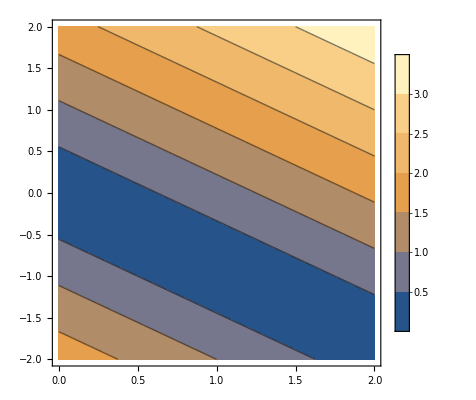

```mathematica
ContourPlot[f[x1,x2], {x1,0,2},{x2,-2,2}, PlotLegends->Automatic]
```